```mathematica
movfile = 0;(*Set to 1 to generate movie files*)
```

```mathematica
(*Default param values*)
aval =3.5;
bval =0.5;
tauval = 10;
Fextval = 0;
gammaval = 0;
mval = 1;
```

```mathematica
kval1 =2.8;
kval2 = 3.4;
kval3 = 4;
```

```mathematica
(************************kval1***************)
```

```mathematica
trange =10^2;
```

```mathematica
fptsln = Solve[{0==-kval1*xstar-(xstar-fstar)^3+aval*(xstar-fstar),0==-fstar/tauval+bval*xstar/tauval},{xstar,fstar}](*Find a solution with a real value for x*)
xfpt = Select[xstar/.fptsln,Abs[Im[#]]<10^-10&][[1]]
ffpt = fstar/.Flatten[fptsln[[Flatten[Position[xstar/.fptsln,xfpt]]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xstar→0.,fstar→0.},{xstar→0.-2.89828 ⅈ,fstar→0.-1.44914 ⅈ},{xstar→0.+2.89828 ⅈ,fstar→0.+1.44914 ⅈ}}

0.

0.

```mathematica
(*Spiral in*)
tres = 10^-2;
{xf1,ff1,vf1}={x,f,v}/.NDSolve[{x'[t]==v[t],mval*v'[t]==-(1+gammaval)*v[t]-kval1*x[t]-(x[t]-f[t])^3+aval*(x[t]-f[t]),f'[t]==-f[t]/tauval+bval*x[t]/tauval,x[0]==xfpt+1.2,f[0]==ffpt+0.5,v[0]==0+1},{x,f,v},{t,0,trange},MaxSteps->50000000,MaxStepSize->tres][[1]]
```

{InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>]}

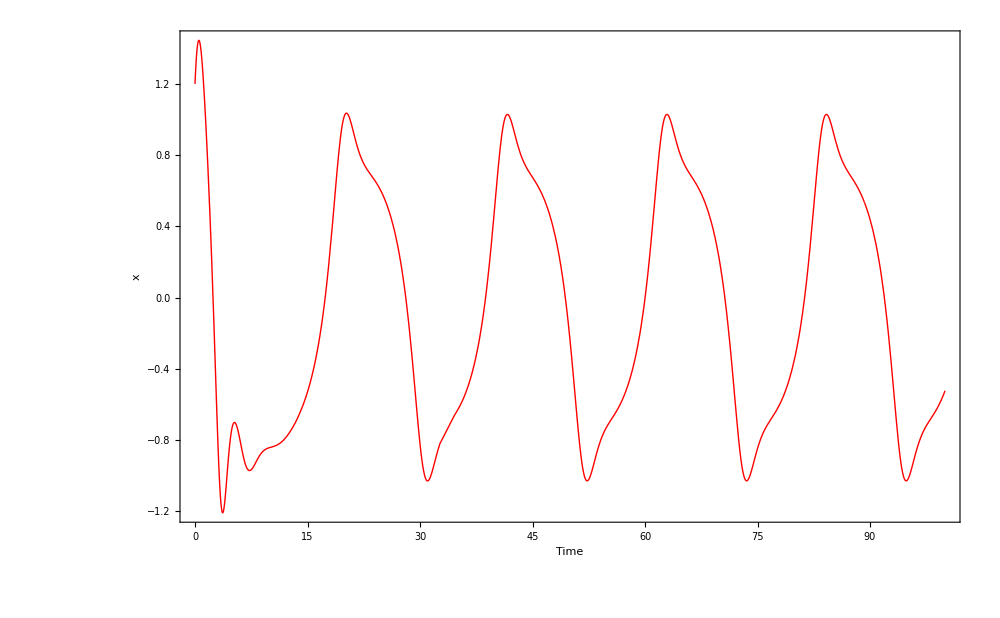

```mathematica
Plot[{xf1[t]},{t,0,trange},MaxRecursion-> 15,AspectRatio->2/(1+Sqrt[5]),PlotRange->{{0,trange},All},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["Time",48,FontFamily->"Helvetica"],Style["x",48,FontFamily->"Helvetica"]},LabelStyle->{48,FontFamily->"Helvetica"},FrameTicksStyle->Thickness[0.004],FrameStyle->Thickness[0.004],Axes->False,ImageSize->1000]
```

```mathematica
fmax = 1.5;
xmax = 1.5;
vmax = 1.5;
Animate[Show[ParametricPlot3D[{xf1[t],ff1[t],vf1[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf1[a],ff1[a],vf1[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2},AnimationRunning->False,DefaultDuration->10,AnimationRepetitions->1]
```

```mathematica
If[movfile ==1,spiralintoLC =Table[Show[ParametricPlot3D[{xf1[t],ff1[t],vf1[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf1[a],ff1[a],vf1[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2}];
Export["ONHspiralintoLC.mov",spiralintoLC];,Null]
```

```mathematica
(*Spiral out*)
{xf1b,ff1b,vf1b}={x,f,v}/.NDSolve[{x'[t]==v[t],mval*v'[t]==-(1+gammaval)*v[t]-kval1*x[t]-(x[t]-f[t])^3+aval*(x[t]-f[t]),f'[t]==-f[t]/tauval+bval*x[t]/tauval,x[0]==xfpt+10^-2,f[0]==ffpt,v[0]==0},{x,f,v},{t,0,trange},MaxSteps->50000000,MaxStepSize->tres][[1]]
```

{InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>]}

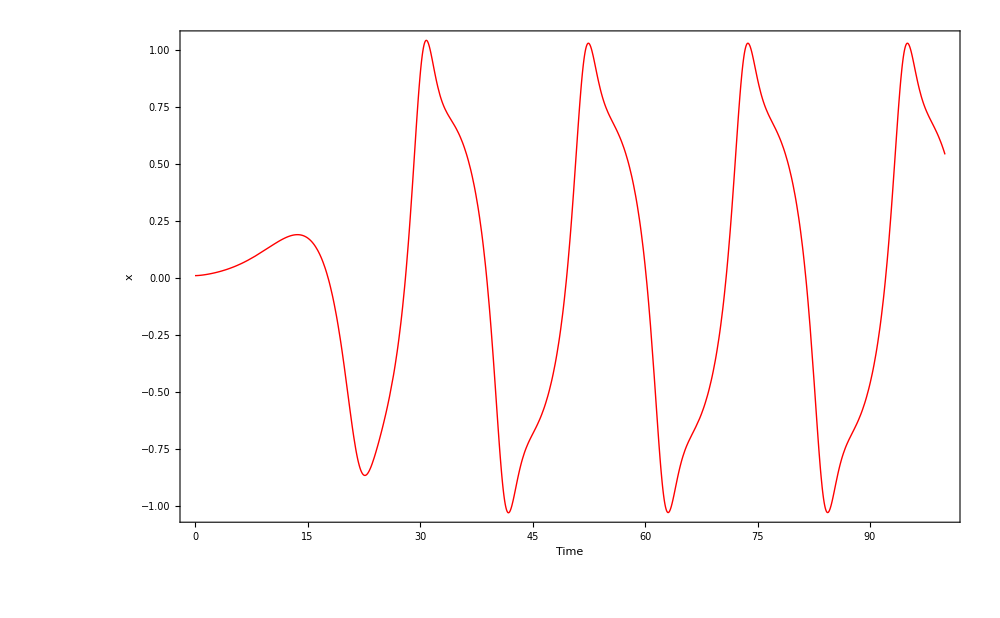

```mathematica
Plot[{xf1b[t]},{t,0,trange},MaxRecursion-> 15,AspectRatio->2/(1+Sqrt[5]),PlotRange->{{0,trange},All},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["Time",48,FontFamily->"Helvetica"],Style["x",48,FontFamily->"Helvetica"]},LabelStyle->{48,FontFamily->"Helvetica"},FrameTicksStyle->Thickness[0.004],FrameStyle->Thickness[0.004],Axes->False,ImageSize->1000]
```

```mathematica
fmax = 1.5;
xmax = 1.5;
vmax = 1.5;
Animate[Show[ParametricPlot3D[{xf1b[t],ff1b[t],vf1b[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf1b[a],ff1b[a],vf1b[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2},AnimationRate->10,AnimationRunning->False]
```

```mathematica
If[movfile == 1,
spiralouttoLC = Table[Show[ParametricPlot3D[{xf1b[t],ff1b[t],vf1b[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf1b[a],ff1b[a],vf1b[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2}];
Export["ONHspiralouttoLC.mov",spiralouttoLC];,Null]
```

```mathematica
(************************kval2***************)
```

```mathematica
trange =10^2;
```

```mathematica
fptsln = Solve[{0==-kval2*xstar-(xstar-fstar)^3+aval*(xstar-fstar),0==-fstar/tauval+bval*xstar/tauval},{xstar,fstar}](*Find a solution with a real value for x*)
xfpt = Select[xstar/.fptsln,Abs[Im[#]]<10^-10&][[1]]
ffpt = fstar/.Flatten[fptsln[[Flatten[Position[xstar/.fptsln,xfpt]]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xstar→0.,fstar→0.},{xstar→0.-3.63318 ⅈ,fstar→0.-1.81659 ⅈ},{xstar→0.+3.63318 ⅈ,fstar→0.+1.81659 ⅈ}}

0.

0.

```mathematica
{xf2,ff2,vf2}={x,f,v}/.NDSolve[{x'[t]==v[t],mval*v'[t]==-(1+gammaval)*v[t]-kval2*x[t]-(x[t]-f[t])^3+aval*(x[t]-f[t]),f'[t]==-f[t]/tauval+bval*x[t]/tauval,x[0]==xfpt+0.5,f[0]==ffpt+0.5,v[0]==0+0.5},{x,f,v},{t,0,trange},MaxSteps->50000000,MaxStepSize->tres][[1]]
```

{InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>]}

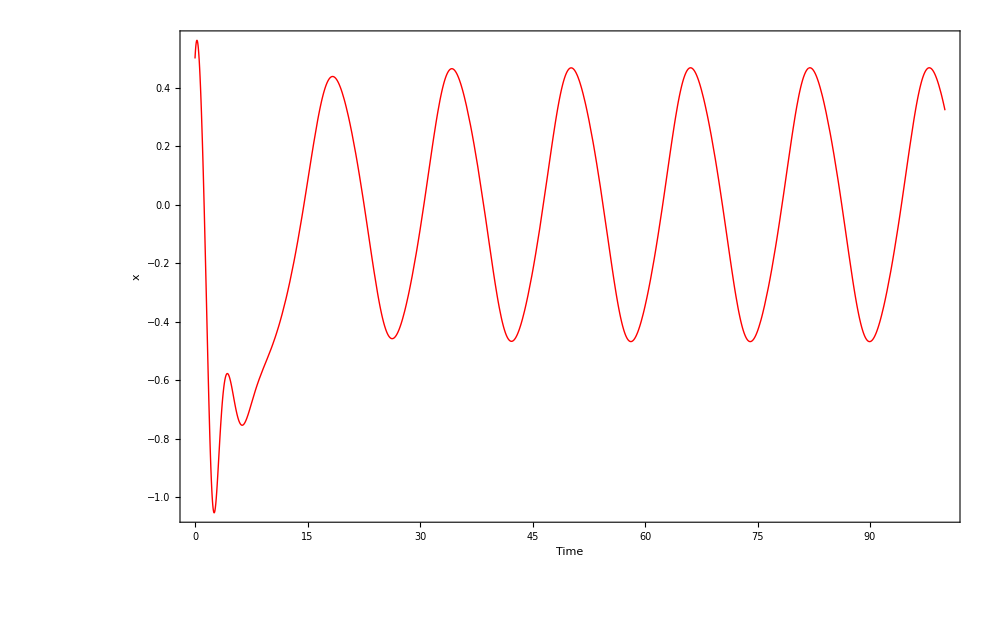

```mathematica
Plot[{xf2[t]},{t,0,trange},MaxRecursion-> 15,AspectRatio->2/(1+Sqrt[5]),PlotRange->{{0,trange},All},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["Time",48,FontFamily->"Helvetica"],Style["x",48,FontFamily->"Helvetica"]},LabelStyle->{48,FontFamily->"Helvetica"},FrameTicksStyle->Thickness[0.004],FrameStyle->Thickness[0.004],Axes->False,ImageSize->1000]
```

```mathematica
fmax = 1.5;
xmax = 1.5;
vmax = 1.5;
Animate[Show[ParametricPlot3D[{xf2[t],ff2[t],vf2[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf2[a],ff2[a],vf2[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2},AnimationRate->10,AnimationRunning->False]
```

```mathematica
If[movfile == 1,
ONHspiralintoLCnearHopf = Table[Show[ParametricPlot3D[{xf2[t],ff2[t],vf2[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf2[a],ff2[a],vf2[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2}];
Export["ONHspiralintoLCnearHopf.mov",ONHspiralintoLCnearHopf];,Null]
```

```mathematica
(************************kval3***************)
```

```mathematica
trange =10^2;
```

```mathematica
fptsln = Solve[{0==-kval3*xstar-(xstar-fstar)^3+aval*(xstar-fstar),0==-fstar/tauval+bval*xstar/tauval},{xstar,fstar}](*Find a solution with a real value for x*)
xfpt = Select[xstar/.fptsln,Abs[Im[#]]<10^-10&][[1]]
ffpt = fstar/.Flatten[fptsln[[Flatten[Position[xstar/.fptsln,xfpt]]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xstar→0.,fstar→0.},{xstar→0.-4.24264 ⅈ,fstar→0.-2.12132 ⅈ},{xstar→0.+4.24264 ⅈ,fstar→0.+2.12132 ⅈ}}

0.

0.

```mathematica
{xf3,ff3,vf3}={x,f,v}/.NDSolve[{x'[t]==v[t],mval*v'[t]==-(1+gammaval)*v[t]-kval3*x[t]-(x[t]-f[t])^3+aval*(x[t]-f[t]),f'[t]==-f[t]/tauval+bval*x[t]/tauval,x[0]==xfpt+0.5,f[0]==ffpt+0.5,v[0]==0+0.5},{x,f,v},{t,0,trange},MaxSteps->50000000,MaxStepSize->tres][[1]]
```

{InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>]}

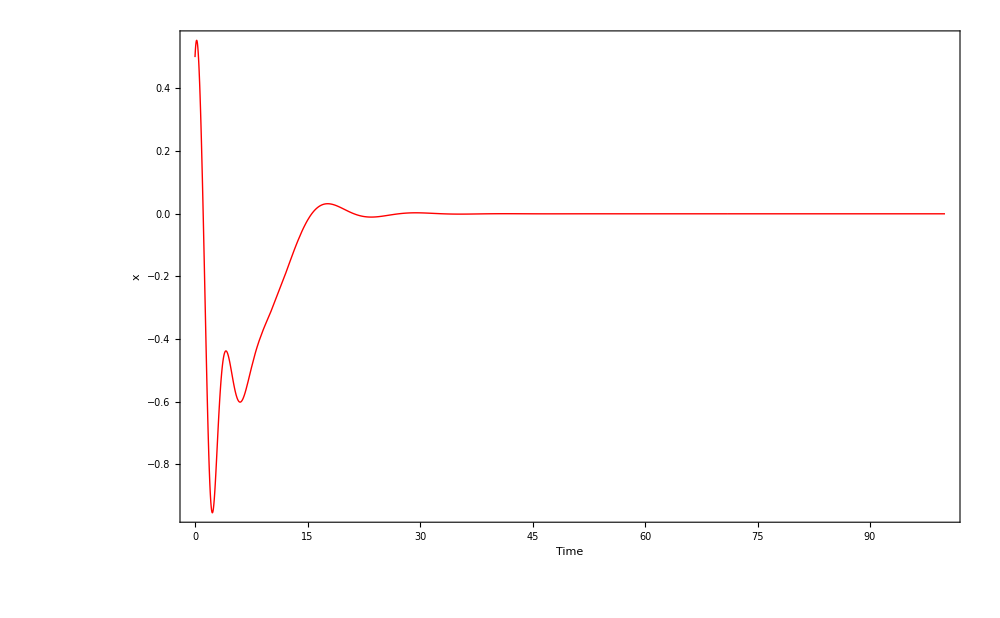

```mathematica
Plot[{xf3[t]},{t,0,trange},MaxRecursion-> 15,AspectRatio->2/(1+Sqrt[5]),PlotRange->{{0,trange},All},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["Time",48,FontFamily->"Helvetica"],Style["x",48,FontFamily->"Helvetica"]},LabelStyle->{48,FontFamily->"Helvetica"},FrameTicksStyle->Thickness[0.004],FrameStyle->Thickness[0.004],Axes->False,ImageSize->1000]
```

```mathematica
fmax = 1.5;
xmax = 1.5;
vmax = 1.5;
Animate[Show[ParametricPlot3D[{xf3[t],ff3[t],vf3[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf3[a],ff3[a],vf3[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2},AnimationRate->10,AnimationRunning->False]
```

```mathematica
If[movfile == 1,
ONHspiralintostableFP = Table[Show[ParametricPlot3D[{xf3[t],ff3[t],vf3[t]},{t,-$MachineEpsilon,a},AspectRatio->1,MaxRecursion->5,PlotStyle->{Thick,Red},LabelStyle->24,AxesStyle->Thick],Graphics3D[{{Green,Sphere[{xf3[a],ff3[a],vf3[a]},0.1]}}],AxesLabel->{x,f,v},PlotRange->{{-fmax,fmax},{-fmax,fmax},{-fmax,fmax}}],{a,0,trange,2}];
Export["ONHspiralintostableFP.mov",ONHspiralintostableFP];,Null]
```